```mathematica
(*Set your directory to where the mathematica notebook is saved*)
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*Import simulated data sets: data3 is for k=0.001, Subscript[p, f]=6 x10^-6 and Subscript[μ, C]=0.01; data2 is for k=0.005, Subscript[p, f]=6 x10^-8 and Subscript[μ, C]=0.1; data1 is for k=0.2, Subscript[p, f]=5 x10^-10 and Subscript[μ, C]=0.001 such that IFR=1.5% and μ=0.87*10^-5*)
data1=Import["data\\K1FM9E-06DMk0.2ICIpf5E-10mC0.001.voc","Table","FieldSeparators"->","];
data2=Import["data\\K1FM9E-06DMk0.005ICIpf6E-8mC0.1.voc","Table","FieldSeparators"->","];
data3=Import["data\\K1FM9E-06DMk0.001ICIpf6E-6mC0.01.voc","Table","FieldSeparators"->","];
```

```mathematica
(*For visual purposes, for any simulation run where Subscript[T, i:(i+1)] is infinity (i.e., the (i+1)^th VOC lineage is not produced by the end of the simulation period), we set infinity to be equal to 800*)
genTime=5.2;
infinity=800;
temp={};
deltaMax=infinity/genTime;

totalLineage3={};
totalLineageTimetoFirst3={};
For[i=2,i≤Length[data3],i++,
AppendTo[totalLineage3,Length[data3[[i]]]-1];
AppendTo[totalLineageTimetoFirst3,{Length[data3[[i]]]-1,genTime data3[[i,2]]}]];

(*If total number of lineages is below 1000, it means that some of the runs generated zero VOCs.*)
If[Length[totalLineage3]<1000,totalLineage3=Join[totalLineage3,ConstantArray[0,1000-Length[totalLineage3]]]];

timeBetweenLineage3={};
For[i=2,i≤Length[data3],i++,
If[Length[data3[[i]]]≥2,temp={};
AppendTo[temp,data3[[i,2]]];
For[j=3,j≤Length[data3[[i]]],j++,
AppendTo[temp,data3[[i,j]]-data3[[i,j-1]]]],AppendTo[temp,deltaMax]];
AppendTo[timeBetweenLineage3,temp]];

(*If the (i+1)^th VOC lineage is not produced by the end of the simulation period, set  Subscript[T, i:(i+1)] to infinity*)
For[i=1,i≤Length[timeBetweenLineage3],i++,If[Length[timeBetweenLineage3[[i]]]<5,timeBetweenLineage3[[i]]=Join[timeBetweenLineage3[[i]],ConstantArray[deltaMax,5-Length[timeBetweenLineage3[[i]]]]]]];

gaps3=ConstantArray[{},Max[totalLineage3]];
For[i=1,i≤Length[timeBetweenLineage3],i++,
For[j=1,j≤Length[timeBetweenLineage3[[i]]],j++,
If[timeBetweenLineage3[[i,j]]==deltaMax,AppendTo[gaps3[[j]],deltaMax],AppendTo[gaps3[[j]],timeBetweenLineage3[[i,j]]]]]];

(*repeat the same for data2*)
totalLineage2={};
totalLineageTimetoFirst2={};
For[i=2,i≤Length[data2],i++,
AppendTo[totalLineage2,Length[data2[[i]]]-1];
AppendTo[totalLineageTimetoFirst2,{Length[data2[[i]]]-1,genTime data2[[i,2]]}]];

If[Length[totalLineage2]<1000,totalLineage2=Join[totalLineage2,ConstantArray[0,1000-Length[totalLineage2]]]];

timeBetweenLineage2={};
For[i=2,i≤Length[data2],i++,
If[Length[data2[[i]]]≥2,temp={};
AppendTo[temp,data2[[i,2]]];
For[j=3,j≤Length[data2[[i]]],j++,
AppendTo[temp,data2[[i,j]]-data2[[i,j-1]]]],AppendTo[temp,deltaMax]];
AppendTo[timeBetweenLineage2,temp]];

For[i=1,i≤Length[timeBetweenLineage2],i++,If[Length[timeBetweenLineage2[[i]]]<5,timeBetweenLineage2[[i]]=Join[timeBetweenLineage2[[i]],ConstantArray[deltaMax,5-Length[timeBetweenLineage2[[i]]]]]]];

gaps2=ConstantArray[{},Max[totalLineage2]];
For[i=1,i≤Length[timeBetweenLineage2],i++,
For[j=1,j≤Length[timeBetweenLineage2[[i]]],j++,
If[timeBetweenLineage2[[i,j]]==deltaMax,AppendTo[gaps2[[j]],deltaMax],AppendTo[gaps2[[j]],timeBetweenLineage2[[i,j]]]]]]

(*repeat the same for data1*)
totalLineage1={};
totalLineageTimetoFirst1={};
For[i=2,i≤Length[data1],i++,
AppendTo[totalLineage1,Length[data1[[i]]]-1];
AppendTo[totalLineageTimetoFirst1,{Length[data1[[i]]]-1,genTime data1[[i,2]]}]];

If[Length[totalLineage1]<1000,totalLineage1=Join[totalLineage1,ConstantArray[0,1000-Length[totalLineage1]]]];

timeBetweenLineage1={};
For[i=2,i≤Length[data1],i++,
If[Length[data1[[i]]]≥2,temp={};
AppendTo[temp,data1[[i,2]]];
For[j=3,j≤Length[data1[[i]]],j++,
AppendTo[temp,data1[[i,j]]-data1[[i,j-1]]]],AppendTo[temp,deltaMax]];
AppendTo[timeBetweenLineage1,temp]];

For[i=1,i≤Length[timeBetweenLineage1],i++,If[Length[timeBetweenLineage1[[i]]]<5,timeBetweenLineage1[[i]]=Join[timeBetweenLineage1[[i]],ConstantArray[deltaMax,5-Length[timeBetweenLineage1[[i]]]]]]];

gaps1=ConstantArray[{},Max[totalLineage1]];
For[i=1,i≤Length[timeBetweenLineage1],i++,
For[j=1,j≤Length[timeBetweenLineage1[[i]]],j++,
If[timeBetweenLineage1[[i,j]]==deltaMax,AppendTo[gaps1[[j]],deltaMax],AppendTo[gaps1[[j]],timeBetweenLineage1[[i,j]]]]]]
```

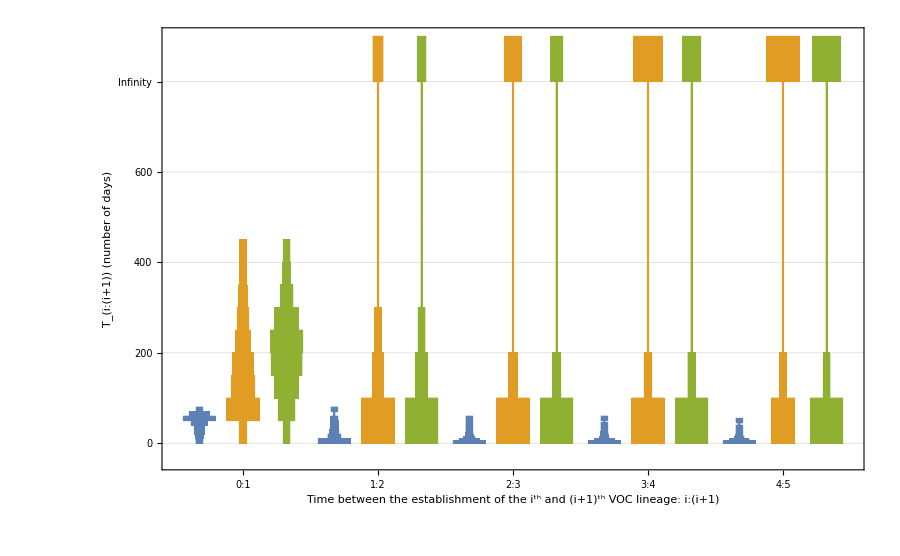

```mathematica
DistributionChart[Table[{genTime gaps1[[1;;Length[gaps1]]][[i]],genTime gaps2[[1;;Length[gaps2]]][[i]],genTime gaps3[[1;;Length[gaps3]]][[i]]},{i,1,5}],ChartLabels->{Table[{StringJoin[ToString[j-1],":",ToString[j]],StringJoin[ToString[j-1],":",ToString[j]],StringJoin[ToString[j-1],":",ToString[j]]},{j,1,6}],Table[StringJoin[ToString[j-1],":",ToString[j]],{j,1,6}],Table[" ",{i,1,6}]},ChartStyle->{ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]],ColorData[97,"ColorList"][[3]]},PlotRange->All,Frame->True,FrameLabel->{"Time between the establishment of the i^th and (i+1)^th VOC lineage: i:(i+1)","T_(i:(i+1)) (number of days)"},FrameStyle->Directive[Black,24],ImageSize->900,PlotTheme->"Detailed",ChartElementFunction->"HistogramDensity",Method->{"BoxWidth"->"Fixed"},FrameTicks->{{{{0,"0"},{100,""},{200,"200"},{300,""},{400,"400"},{500,""},{600,"600"},{infinity,"Infinity"}},{{0,""},{50,""},{100,""},{150,""},{200,""},{infinity,""}}},{Automatic,Automatic}}]
```

```mathematica
(*In the paper, we manually added the enclosed red dashed lines showing the region matching the clustered emergence of 3 VOCs in late 2020*)
```